# Mathematica Lab #2

Type your name here!

DIRECTIONS:  you are ask to complete all of the items below.  For submission, submit your work to the appropriate upload site with the file name:  LastnameMMALab2.nb, for example:  GotwalsMMALab2.nb.  Show ALL of your inputs (commands) and resulting outputs.  Before you submit, EVALUATE YOUR ENTIRE NOTEBOOK, including if it requests to evaluate INITIALIZATION CELLS! 

In this file, I have shown you what the output should look like.  You should DELETE all cells with my output, to be replaced by yours.  Please do not delete the item-ed numbers.

Load the file a comma-separated values file "grades.csv" located at http://chemistry.ncssm.edu/data/grades.csv.  Place this data into a variable called "grades".

```mathematica
grade = Import["http://chemistry.ncssm.edu/data/grades.csv"]
```

{{College.GPA,HS.GPA,SAT,RecLetterQuality},{2.04,2.01,1070,5},{2.56,3.4,1254,6},{3.75,3.68,1466,6},{1.1,1.54,706,4},{3,3.32,1160,5},{0.05,0.33,756,3},{1.38,0.36,1058,2},{1.5,1.97,1008,7},{1.38,2.03,1104,4},{4.01,2.05,1200,7},{1.5,2.13,896,7},{1.29,1.34,848,3},{1.9,1.51,958,5},{3.11,3.12,1246,6},{1.92,2.14,1106,4},{0.81,2.6,790,5},{1.01,1.9,954,4},{3.66,3.06,1500,6},{2,1.6,1046,5},{2.05,1.96,1054,4},{2.6,1.96,1198,6},{2.55,1.56,940,3},{0.38,1.6,456,6},{2.48,1.92,1150,7},{2.74,3.09,636,6},{1.77,0.78,744,5},{1.61,2.12,644,5},{0.99,1.85,842,3},{1.62,1.78,852,5},{2.03,1.03,1170,3},{3.5,3.44,1034,10},{3.18,2.42,1202,5},{2.39,1.74,1018,5},{1.48,1.89,1180,5},{1.54,1.43,952,3},{1.57,1.64,1038,4},{2.46,2.69,1090,6},{2.42,1.79,694,5},{2.11,2.72,1096,6},{2.04,2.15,1114,5},{1.68,2.22,1256,6},{1.64,1.55,1208,5},{2.41,2.34,820,6},{2.1,2.92,1222,4},{1.4,2.1,1120,5},{2.03,1.64,886,4},{1.99,2.83,1126,7},{2.24,1.76,1158,4},{0.45,1.81,676,6},{2.31,2.68,1214,7},{2.41,2.55,1136,6},{2.56,2.7,1264,6},{2.5,1.66,1116,3},{2.92,2.23,1292,4},{2.35,2.01,604,5},{2.82,1.24,854,6},{1.8,1.95,814,6},{1.29,1.73,778,3},{1.68,1.08,800,2},{3.44,3.46,1424,7},{1.9,3.01,950,6},{2.06,0.54,1056,3},{3.3,3.2,956,8},{1.8,1.5,1352,5},{2,1.71,852,5},{1.68,1.99,1168,5},{1.94,2.76,970,6},{0.97,1.56,776,4},{1.12,1.78,854,6},{1.31,1.32,1232,5},{1.68,0.87,1140,6},{3.09,1.75,1084,4},{1.87,1.41,954,2},{2,2.77,1000,4},{2.39,1.78,1084,4},{1.5,1.34,1058,4},{1.82,1.52,816,5},{1.8,2.97,1146,7},{2.01,1.75,1000,6},{1.88,1.64,856,4},{1.64,1.8,798,4},{2.42,3.37,1324,6},{0.22,1.15,704,6},{2.31,1.72,1222,5},{0.95,2.27,948,6},{1.99,2.85,1182,8},{1.86,2.21,1000,6},{1.79,1.94,910,6},{3.02,4.25,1374,9},{1.85,1.83,1014,6},{1.98,2.75,1420,7},{2.15,1.71,400,6},{1.46,2.2,998,7},{2.29,2.13,776,6},{2.39,2.38,1134,7},{1.8,1.64,772,4},{2.64,1.87,1304,6},{2.08,2.53,1212,4},{0.7,1.78,818,6},{0.89,1.2,864,2}}

Display the data as a nice table:

```mathematica
Grid[grade,Frame-> All]
```

College.GPA | HS.GPA | SAT | RecLetterQuality
2.04 | 2.01 | 1070 | 5
2.56 | 3.4 | 1254 | 6
3.75 | 3.68 | 1466 | 6
1.1 | 1.54 | 706 | 4
3 | 3.32 | 1160 | 5
0.05 | 0.33 | 756 | 3
1.38 | 0.36 | 1058 | 2
1.5 | 1.97 | 1008 | 7
1.38 | 2.03 | 1104 | 4
4.01 | 2.05 | 1200 | 7
1.5 | 2.13 | 896 | 7
1.29 | 1.34 | 848 | 3
1.9 | 1.51 | 958 | 5
3.11 | 3.12 | 1246 | 6
1.92 | 2.14 | 1106 | 4
0.81 | 2.6 | 790 | 5
1.01 | 1.9 | 954 | 4
3.66 | 3.06 | 1500 | 6
2 | 1.6 | 1046 | 5
2.05 | 1.96 | 1054 | 4
2.6 | 1.96 | 1198 | 6
2.55 | 1.56 | 940 | 3
0.38 | 1.6 | 456 | 6
2.48 | 1.92 | 1150 | 7
2.74 | 3.09 | 636 | 6
1.77 | 0.78 | 744 | 5
1.61 | 2.12 | 644 | 5
0.99 | 1.85 | 842 | 3
1.62 | 1.78 | 852 | 5
2.03 | 1.03 | 1170 | 3
3.5 | 3.44 | 1034 | 10
3.18 | 2.42 | 1202 | 5
2.39 | 1.74 | 1018 | 5
1.48 | 1.89 | 1180 | 5
1.54 | 1.43 | 952 | 3
1.57 | 1.64 | 1038 | 4
2.46 | 2.69 | 1090 | 6
2.42 | 1.79 | 694 | 5
2.11 | 2.72 | 1096 | 6
2.04 | 2.15 | 1114 | 5
1.68 | 2.22 | 1256 | 6
1.64 | 1.55 | 1208 | 5
2.41 | 2.34 | 820 | 6
2.1 | 2.92 | 1222 | 4
1.4 | 2.1 | 1120 | 5
2.03 | 1.64 | 886 | 4
1.99 | 2.83 | 1126 | 7
2.24 | 1.76 | 1158 | 4
0.45 | 1.81 | 676 | 6
2.31 | 2.68 | 1214 | 7
2.41 | 2.55 | 1136 | 6
2.56 | 2.7 | 1264 | 6
2.5 | 1.66 | 1116 | 3
2.92 | 2.23 | 1292 | 4
2.35 | 2.01 | 604 | 5
2.82 | 1.24 | 854 | 6
1.8 | 1.95 | 814 | 6
1.29 | 1.73 | 778 | 3
1.68 | 1.08 | 800 | 2
3.44 | 3.46 | 1424 | 7
1.9 | 3.01 | 950 | 6
2.06 | 0.54 | 1056 | 3
3.3 | 3.2 | 956 | 8
1.8 | 1.5 | 1352 | 5
2 | 1.71 | 852 | 5
1.68 | 1.99 | 1168 | 5
1.94 | 2.76 | 970 | 6
0.97 | 1.56 | 776 | 4
1.12 | 1.78 | 854 | 6
1.31 | 1.32 | 1232 | 5
1.68 | 0.87 | 1140 | 6
3.09 | 1.75 | 1084 | 4
1.87 | 1.41 | 954 | 2
2 | 2.77 | 1000 | 4
2.39 | 1.78 | 1084 | 4
1.5 | 1.34 | 1058 | 4
1.82 | 1.52 | 816 | 5
1.8 | 2.97 | 1146 | 7
2.01 | 1.75 | 1000 | 6
1.88 | 1.64 | 856 | 4
1.64 | 1.8 | 798 | 4
2.42 | 3.37 | 1324 | 6
0.22 | 1.15 | 704 | 6
2.31 | 1.72 | 1222 | 5
0.95 | 2.27 | 948 | 6
1.99 | 2.85 | 1182 | 8
1.86 | 2.21 | 1000 | 6
1.79 | 1.94 | 910 | 6
3.02 | 4.25 | 1374 | 9
1.85 | 1.83 | 1014 | 6
1.98 | 2.75 | 1420 | 7
2.15 | 1.71 | 400 | 6
1.46 | 2.2 | 998 | 7
2.29 | 2.13 | 776 | 6
2.39 | 2.38 | 1134 | 7
1.8 | 1.64 | 772 | 4
2.64 | 1.87 | 1304 | 6
2.08 | 2.53 | 1212 | 4
0.7 | 1.78 | 818 | 6
0.89 | 1.2 | 864 | 2

Delete the header row and then extract out each variable and place it into its own variable name, using these variable names:  collegegpa, hsgpa,sat,recs.  Do NOT include the heading as a part of the dataset.

```mathematica
gradenolabels = Delete[grade,1];
{collegegpa,hsgpa,sat,recs} = Transpose[gradenolabels]
```

{{2.04,2.56,3.75,1.1,3,0.05,1.38,1.5,1.38,4.01,1.5,1.29,1.9,3.11,1.92,0.81,1.01,3.66,2,2.05,2.6,2.55,0.38,2.48,2.74,1.77,1.61,0.99,1.62,2.03,3.5,3.18,2.39,1.48,1.54,1.57,2.46,2.42,2.11,2.04,1.68,1.64,2.41,2.1,1.4,2.03,1.99,2.24,0.45,2.31,2.41,2.56,2.5,2.92,2.35,2.82,1.8,1.29,1.68,3.44,1.9,2.06,3.3,1.8,2,1.68,1.94,0.97,1.12,1.31,1.68,3.09,1.87,2,2.39,1.5,1.82,1.8,2.01,1.88,1.64,2.42,0.22,2.31,0.95,1.99,1.86,1.79,3.02,1.85,1.98,2.15,1.46,2.29,2.39,1.8,2.64,2.08,0.7,0.89},{2.01,3.4,3.68,1.54,3.32,0.33,0.36,1.97,2.03,2.05,2.13,1.34,1.51,3.12,2.14,2.6,1.9,3.06,1.6,1.96,1.96,1.56,1.6,1.92,3.09,0.78,2.12,1.85,1.78,1.03,3.44,2.42,1.74,1.89,1.43,1.64,2.69,1.79,2.72,2.15,2.22,1.55,2.34,2.92,2.1,1.64,2.83,1.76,1.81,2.68,2.55,2.7,1.66,2.23,2.01,1.24,1.95,1.73,1.08,3.46,3.01,0.54,3.2,1.5,1.71,1.99,2.76,1.56,1.78,1.32,0.87,1.75,1.41,2.77,1.78,1.34,1.52,2.97,1.75,1.64,1.8,3.37,1.15,1.72,2.27,2.85,2.21,1.94,4.25,1.83,2.75,1.71,2.2,2.13,2.38,1.64,1.87,2.53,1.78,1.2},{1070,1254,1466,706,1160,756,1058,1008,1104,1200,896,848,958,1246,1106,790,954,1500,1046,1054,1198,940,456,1150,636,744,644,842,852,1170,1034,1202,1018,1180,952,1038,1090,694,1096,1114,1256,1208,820,1222,1120,886,1126,1158,676,1214,1136,1264,1116,1292,604,854,814,778,800,1424,950,1056,956,1352,852,1168,970,776,854,1232,1140,1084,954,1000,1084,1058,816,1146,1000,856,798,1324,704,1222,948,1182,1000,910,1374,1014,1420,400,998,776,1134,772,1304,1212,818,864},{5,6,6,4,5,3,2,7,4,7,7,3,5,6,4,5,4,6,5,4,6,3,6,7,6,5,5,3,5,3,10,5,5,5,3,4,6,5,6,5,6,5,6,4,5,4,7,4,6,7,6,6,3,4,5,6,6,3,2,7,6,3,8,5,5,5,6,4,6,5,6,4,2,4,4,4,5,7,6,4,4,6,6,5,6,8,6,6,9,6,7,6,7,6,7,4,6,4,6,2}}

Put variables hsgpa and collegegpa into ONE list with the variable name: hscollege:

```mathematica
hscollege = Transpose[{hsgpa,collegegpa}]
```

{{2.01,2.04},{3.4,2.56},{3.68,3.75},{1.54,1.1},{3.32,3},{0.33,0.05},{0.36,1.38},{1.97,1.5},{2.03,1.38},{2.05,4.01},{2.13,1.5},{1.34,1.29},{1.51,1.9},{3.12,3.11},{2.14,1.92},{2.6,0.81},{1.9,1.01},{3.06,3.66},{1.6,2},{1.96,2.05},{1.96,2.6},{1.56,2.55},{1.6,0.38},{1.92,2.48},{3.09,2.74},{0.78,1.77},{2.12,1.61},{1.85,0.99},{1.78,1.62},{1.03,2.03},{3.44,3.5},{2.42,3.18},{1.74,2.39},{1.89,1.48},{1.43,1.54},{1.64,1.57},{2.69,2.46},{1.79,2.42},{2.72,2.11},{2.15,2.04},{2.22,1.68},{1.55,1.64},{2.34,2.41},{2.92,2.1},{2.1,1.4},{1.64,2.03},{2.83,1.99},{1.76,2.24},{1.81,0.45},{2.68,2.31},{2.55,2.41},{2.7,2.56},{1.66,2.5},{2.23,2.92},{2.01,2.35},{1.24,2.82},{1.95,1.8},{1.73,1.29},{1.08,1.68},{3.46,3.44},{3.01,1.9},{0.54,2.06},{3.2,3.3},{1.5,1.8},{1.71,2},{1.99,1.68},{2.76,1.94},{1.56,0.97},{1.78,1.12},{1.32,1.31},{0.87,1.68},{1.75,3.09},{1.41,1.87},{2.77,2},{1.78,2.39},{1.34,1.5},{1.52,1.82},{2.97,1.8},{1.75,2.01},{1.64,1.88},{1.8,1.64},{3.37,2.42},{1.15,0.22},{1.72,2.31},{2.27,0.95},{2.85,1.99},{2.21,1.86},{1.94,1.79},{4.25,3.02},{1.83,1.85},{2.75,1.98},{1.71,2.15},{2.2,1.46},{2.13,2.29},{2.38,2.39},{1.64,1.8},{1.87,2.64},{2.53,2.08},{1.78,0.7},{1.2,0.89}}

Show a boxplot for the variable recs (recommendation letters)

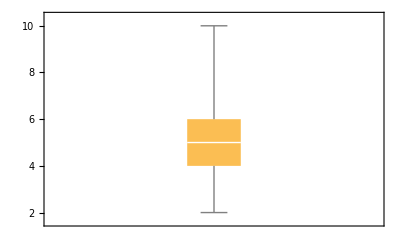

```mathematica
BoxWhiskerChart[recs]
```

Plot hscollege as a graph with dots.  Label the axes as shown in the graph below:

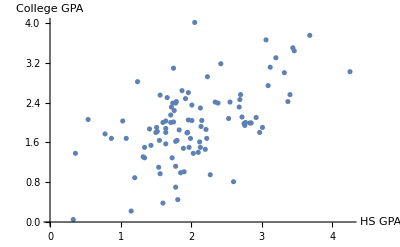

```mathematica
ListPlot[hscollege, 
AxesLabel->{"HS GPA", "College GPA"}]
```

Perform a linear regression on the hscollege data set:

```mathematica
Clear[x] (*note that I cleared x for you, just in case it's in memory *)
reg = LinearModelFit[hscollege,x,x]
```

FittedModel[…]

Plot the original data points in hscollege with the line of best fit as an overlay:

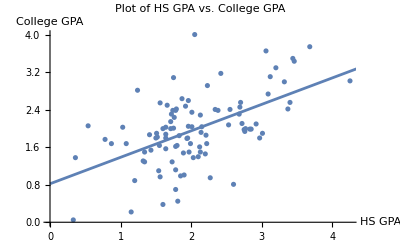

```mathematica
Show [
ListPlot[hscollege,
PlotLabel -> "Plot of HS GPA vs. College GPA",
AxesLabel->{"HS GPA", "College GPA"}],
Plot[reg["BestFit"], {x,0,5}]
]
```